# Probabilités et Statistique II Chapitre 6. Lois continues de probabilités

Jamel Saadaoui

University of Strasbourg, BETA,CNRS

https://www.jamelsaadaoui.com/

Uniform Distribution

```mathematica
PDF[UniformDistribution[{a,b}],x]
```

Piecewise[{{1/(-a+b), a≤x≤b}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{1/(-a+b),a≤x≤b}},0]]
```

Piecewise[{{1/(-a+b), a-x≤0&&b-x≥0}, {0, True}}]

```mathematica
Simplify[Piecewise[{{1/(-a+b),a≤x≤b}},0]]
```

Piecewise[{{1/(-a+b), a≤x≤b}, {0, True}}]

```mathematica
d=UniformDistribution[{1,11}]
```

UniformDistribution[{1,11}]

```mathematica
PDF[d,x]
```

Piecewise[{{1/10, 1≤x≤11}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{1/10,1≤x≤11}},0]]
```

Piecewise[{{1/10, 1≤x≤11}, {0, True}}]

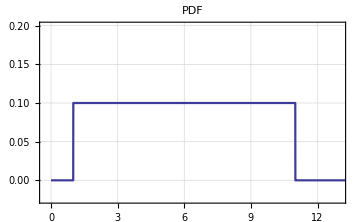

```mathematica
pdf=Plot[PiecewiseExpand[Piecewise[{{1/10,1≤x≤11}},0]],{x,0,15},PlotLabel->"PDF",PlotStyle->ColorData[1,1],GridLines->Automatic,PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-0.25,13},{-0.025,0.2}}]
```

```mathematica
CDF[d,x]
```

Piecewise[{{1/10 (-1+x), 1≤x≤11}, {1, x>11}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{1/10 (-1+x),1≤x≤11},{1,x>11}},0]]
```

Piecewise[{{1, x>11}, {1/10 (-1+x), 1≤x≤11}, {0, True}}]

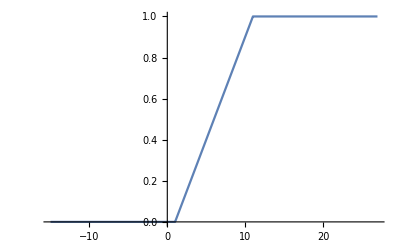

```mathematica
Plot[Piecewise[{{1,x>11},{1/10 (-1+x),1≤x≤11}},0],{x,-15.,27.}]
```

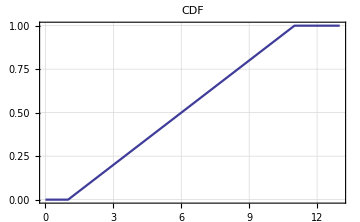

```mathematica
cdf=Plot[PiecewiseExpand[Piecewise[{{1,x>11},{1/10 (-1+x),1≤x≤11}},0]],{x,0,13},PlotLabel->"CDF",PlotStyle->ColorData[1,1],GridLines->Automatic,PlotTheme->"Scientific",ImageSize->Medium]
```

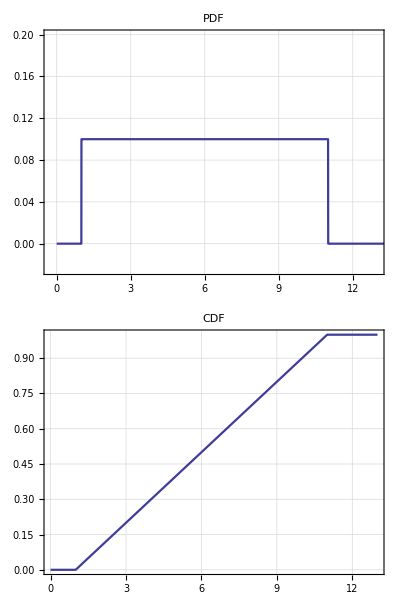

```mathematica
Grid[{{pdf},{cdf}}]
```

```mathematica
Insert[%40,Alignment->Right,2]
```

-Graphics-

## Mean Uniform Distribution

The aim is to replicate the demonstration than can be found here : 
https://en.wikibooks.org/wiki/Statistics/Distributions/Uniform

```mathematica
Mean[UniformDistribution[{a,b}]]
```

(a+b)/2

## Variance Uniform Distribution

The aim is to replicate the demonstration than can be found here : 
https://en.wikibooks.org/wiki/Statistics/Distributions/Discrete_Uniform

```mathematica
Variance[UniformDistribution[{a,b}]]
```

1/12 (-a+b)^2

Exponential Distribution

```mathematica
exp=ExponentialDistribution[α]
```

ExponentialDistribution[α]

```mathematica
PDF[exp,x]
```

Piecewise[{{ⅇ^(-x α) α, x≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{ⅇ^(-x α) α,x≥0}},0]]
```

Piecewise[{{ⅇ^(-x α) α, x≥0}, {0, True}}]

```mathematica
Manipulate[Plot[PiecewiseExpand[Piecewise[{{ⅇ^(-x α) α,x≥0}},0]],{x,-1,5.895879734614027},PlotRange->{{-1,7},{-1,2}}],{α,0.5,2}]
```

```mathematica
CDF[exp,x]
```

Piecewise[{{1-ⅇ^(-x α), x≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{1-ⅇ^(-x α),x≥0}},0]]
```

Piecewise[{{ⅇ^(-x α) (-1+ⅇ^(x α)), x≥0}, {0, True}}]

```mathematica
Manipulate[Plot[PiecewiseExpand[Piecewise[{{1-ⅇ^(-x α) ,x≥0}},0]],{x,-1,10},PlotRange->{{-1,8},{-1,1}}],{α,0.5,2}]
```

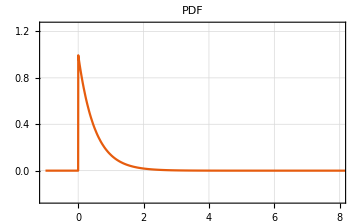

```mathematica
pdf=Plot[PiecewiseExpand[Piecewise[{{ⅇ^(-x 2),x≥0}},0]],{x,-1,10},PlotRange->{{-1,8},{-0.25,1.25}},GridLines->Automatic,PlotLabel->"PDF",PlotTheme->"Scientific",ImageSize->Medium]
```

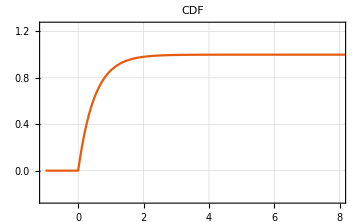

```mathematica
cdf=Plot[PiecewiseExpand[Piecewise[{{1-ⅇ^(-x 2),x≥0}},0]],{x,-1,10},PlotRange->{{-1,8},{-0.25,1.25}},GridLines->Automatic,PlotLabel->"CDF",PlotTheme->"Scientific",ImageSize->Medium]
```

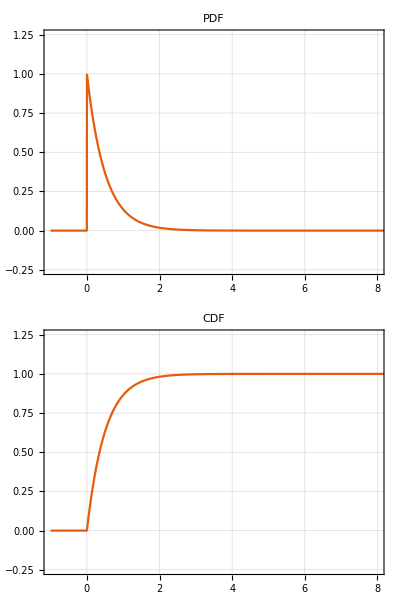

```mathematica
Grid[{{pdf},{cdf}}]
```

Demonstration (Mean)
https://en.wikibooks.org/wiki/Statistics/Distributions/Exponential

```mathematica
Mean[ExponentialDistribution[λ]]
```

1/λ

Demonstration (Variance)
https://www.statlect.com/probability-distributions/exponential-distribution

```mathematica
Variance[ExponentialDistribution[λ]]
```

1/λ^2

```mathematica
Integrate[(λ Power[x,2])/Power[E,(λ x)],{x,0,Infinity}]
```

ConditionalExpression[2/λ^2, Re[λ]>0]

Normal Distribution

```mathematica
PDF[NormalDistribution[μ,σ]]
```

Function[x,(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)]

```mathematica
d=NormalDistribution[μ,σ]
```

NormalDistribution[μ,σ]

```mathematica
PDF[d,x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
PDF[d,x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Manipulate[Plot[(ⅇ^(-(x-μ)^2/(2 1^2)))/(√(2 π) 1),{x,-10,10},PlotRange->{{-10,10},{-0.25,0.5}}],{μ,0,5}]
```

```mathematica
Manipulate[Plot[(ⅇ^(-(x-0)^2/(2 σ^2)))/(√(2 π) σ),{x,-10,10},PlotRange->{{-10,10},{-0.25,0.5}}],{σ,1,5}]
```

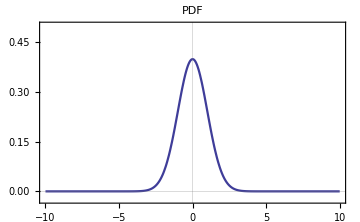

```mathematica
pdf=Plot[(ⅇ^(-(x-0)^2/(2 1^2)))/(√(2 π) 1),{x,-10,10},PlotLabel->"PDF",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-10,10},{-0.025,0.5}}]
```

```mathematica
CDF[d,x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
Manipulate[Plot[1/2 Erfc[(-x+μ)/(√2 1)],{x,-10,10}],{μ,-5.316227766016837,5.316227766016837}]
```

```mathematica
Manipulate[Plot[1/2 Erfc[(-x+0)/(√2  σ)],{x,-15,15}],{ σ,1,5}]
```

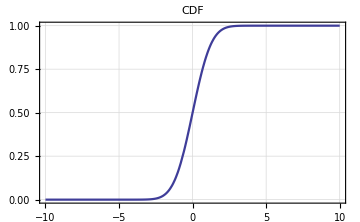

```mathematica
cdf=Plot[1/2 Erfc[(-x+0)/(√2 1)],{x,-10,10},PlotStyle->ColorData[1,1],PlotLabel->"CDF",GridLines->Automatic,PlotTheme->"Scientific",ImageSize->Medium]
```

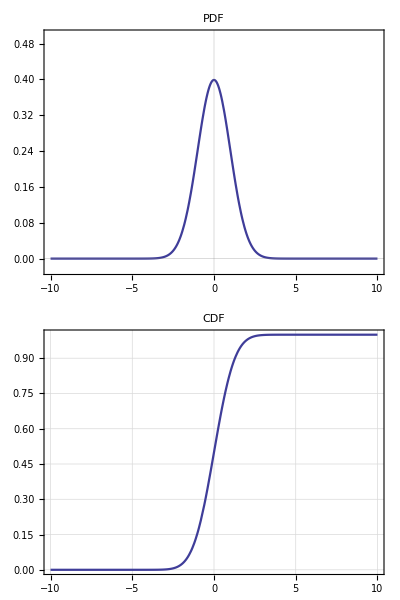

```mathematica
Grid[{{pdf},{cdf}}]
```

## Demonstration (Mean)

```mathematica
(* (1) Write the expression for the Mean:  ∑_(i=0)^n f(Subscript[x, i])×(Subscript[x, i]) *)
```

https://www.statlect.com/probability-distributions/normal-distribution

Demonstration (Variance)

```mathematica
(* (1) Write the expression for the "Squared Mean":  ∑_(i=0)^n f(Subscript[x, i])×(Subscript[x, i])^2 *)
```

https://www.statlect.com/probability-distributions/normal-distribution

Properties

https://www.ztable.net/

Properties

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

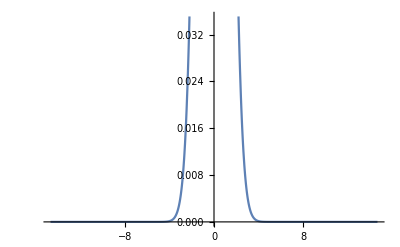

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
"interactive plot"%12DynamicModule[{xc,dx},Manipulate[Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,xc-dx,xc+dx}],{{xc,0.,"center"},-88.18163074019441,88.18163074019441},{{dx,14.696938456699069,"zoom"},88.18163074019441,0.881816307401944}],DynamicModuleValues:>{}]
```

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

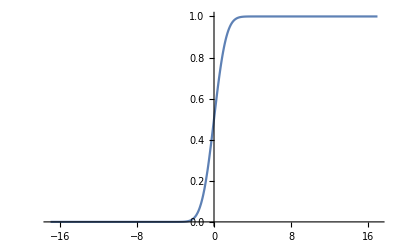

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

```mathematica
CDF[NormalDistribution[0,1],1]
```

1/2 Erfc[-1/(√2)]

```mathematica
N[1/2 Erfc[-1/(√2)]]
```

0.841345

```mathematica
CDF[NormalDistribution[0,1],1.5]
```

0.933193

```mathematica
CDF[NormalDistribution[0,1],1.54]
```

0.93822

```mathematica
CDF[NormalDistribution[0,1],-1.92]
```

0.0274289

```mathematica
1-CDF[NormalDistribution[0,1],1.92]
```

0.0274289

```mathematica
CDF[NormalDistribution[0,1],2]-CDF[NormalDistribution[0,1],-1]
```

-1/2 Erfc[1/(√2)]+1/2 Erfc[-√2]

```mathematica
N[-1/2 Erfc[1/(√2)]+1/2 Erfc[-√2]]
```

https://www.wolframalpha.com/input?i=normal+distribution+calculator&assumption=%7B%22F%22%2C+%22NormalProbabilities%22%2C+%22mu%22%7D+-%3E%220%22&assumption=%7B%22F%22%2C+%22NormalProbabilities%22%2C+%22sigma%22%7D+-%3E%221%22&assumption=%7B%22F%22%2C+%22NormalProbabilities%22%2C+%22pr%22%7D+-%3E%220.95%22